New in CIP 1.1

Data Cleaning or Splitting

This tutorial demonstrates new functions of CIP version 1.1 that complement the discussion in textbook

Achim Zielesny, From Curve Fitting to Machine Learning: An illustrative Guide to scientific Data Analysis and Computational Intelligence, Berlin 2011. (Springer: Intelligent Systems Reference Library, Volume 18).

CIP is available at http://www.gnwi.de.

```mathematica
Clear["Global`*"];
<<CIP`Utility`
<<CIP`ExperimentalData`
<<CIP`DataTransformation`
<<CIP`Cluster`
```

An inspection of data sets and possible cleaning operations are often necessary to avoid subtle errors during data analysis. If a data set is well formed

```mathematica
input1={10.,11.,12.,13.};output1={101.,102.};ioPair1={input1,output1};
input2={20.,21.,22.,23.};output2={201.,202.};ioPair2={input2,output2};
input3={30.,31.,32.,33.};output3={301.,302.};ioPair3={input3,output3};
dataSet={ioPair1,ioPair2,ioPair3};
MatrixForm[CIP`DataTransformation`CleanDataSet[dataSet]]
```

({10.,11.,12.,13.} | {101.,102.}
{20.,21.,22.,23.} | {201.,202.}
{30.,31.,32.,33.} | {301.,302.})

a CleanDataSet operation does no affect its structure and values. If components are integer instead of real numbers

```mathematica
input1={10,11,12,13};output1={101.,102.};ioPair1={input1,output1};
input2={20.,21.,22.,23.};output2={201.,202.};ioPair2={input2,output2};
input3={30.,31.,32.,33.};output3={301.,302.};ioPair3={input3,output3};
dataSet={ioPair1,ioPair2,ioPair3};
MatrixForm[CIP`DataTransformation`CleanDataSet[dataSet]]
```

({10.,11.,12.,13.} | {101.,102.}
{20.,21.,22.,23.} | {201.,202.}
{30.,31.,32.,33.} | {301.,302.})

they are converted to real numbers. If an input or output component value is not defined

```mathematica
input1={10.,NaN,12.,13.};output1={101.,102.};ioPair1={input1,output1};
input2={20.,21.,22.,23.};output2={201.,202.};ioPair2={input2,output2};
input3={30.,31.,32.,33.};output3={301.,302.};ioPair3={input3,output3};
dataSet={ioPair1,ioPair2,ioPair3};
MatrixForm[CIP`DataTransformation`CleanDataSet[dataSet]]
```

({10.,12.,13.} | {101.,102.}
{20.,22.,23.} | {201.,202.}
{30.,32.,33.} | {301.,302.})

the whole corresponding column is removed. If only the corresponding I/O pair is to be removed the RemoveNonNumberIoPairs operation should be applied:

```mathematica
input1={10.,NaN,12.,13.};output1={101.,102.};ioPair1={input1,output1};
input2={20.,21.,22.,23.};output2={201.,202.};ioPair2={input2,output2};
input3={30.,31.,32.,33.};output3={301.,302.};ioPair3={input3,output3};
dataSet={ioPair1,ioPair2,ioPair3};
MatrixForm[CIP`DataTransformation`RemoveNonNumberIoPairs[dataSet]]
```

({20.,21.,22.,23.} | {201.,202.}
{30.,31.,32.,33.} | {301.,302.})

If an input component is identical in all I/O pairs

```mathematica
input1={10.,11.,12.,13.};output1={101.,102.};ioPair1={input1,output1};
input2={20.,11.,22.,23.};output2={201.,202.};ioPair2={input2,output2};
input3={30.,11.,32.,33.};output3={301.,302.};ioPair3={input3,output3};
dataSet={ioPair1,ioPair2,ioPair3};
MatrixForm[CIP`DataTransformation`CleanDataSet[dataSet]]
```

({10.,12.,13.} | {101.,102.}
{20.,22.,23.} | {201.,202.}
{30.,32.,33.} | {301.,302.})

the whole corresponding column is removed. Removing this kind of redundant information does not affect e.g. clustering operations:

```mathematica
imageClassificationDataSet=CIP`ExperimentalData`GetFacesWhiteImageDataSet[];
classificationDataSet=CIP`DataTransformation`ConvertImageDataSet[imageClassificationDataSet];
classIndexMinMaxList=CIP`DataTransformation`SortClassificationDataSet[classificationDataSet][[2]];
inputs=CIP`Utility`GetInputsOfDataSet[classificationDataSet];
Length[inputs[[1]]]
```

900

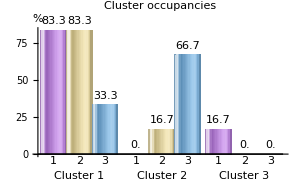

```mathematica
numberOfClusters=3;
clusterInfo=CIP`Cluster`GetFixedNumberOfClusters[inputs,numberOfClusters];
clusterOccupancies=CIP`Cluster`GetClusterOccupancies[classIndexMinMaxList,clusterInfo];
CIP`Cluster`ShowClusterOccupancies[clusterOccupancies]
```

Removing identical input components

```mathematica
cleanedClassificationDataSet=CIP`DataTransformation`CleanDataSet[classificationDataSet];
cleanedInputs=CIP`Utility`GetInputsOfDataSet[cleanedClassificationDataSet];
Length[cleanedInputs[[1]]]
```

888

does not affect the clustering result:

```mathematica
numberOfClusters=3;
clusterInfo=CIP`Cluster`GetFixedNumberOfClusters[cleanedInputs,numberOfClusters];
clusterOccupancies=CIP`Cluster`GetClusterOccupancies[classIndexMinMaxList,clusterInfo];
CIP`Cluster`ShowClusterOccupancies[clusterOccupancies]
```

-Graphics-

A data set

```mathematica
pureOriginalFunction=Function[{x,y},1.9*(1.35+Exp[x]*Sin[13.0*(x-0.6)^2]*Exp[-y]* Sin[7.0*y])];
xRange={0.0,1.5};
yRange={0.0,1.5};
numberOfDataPerDimension=100;
standardDeviationRange={0.1,0.1};
dataSet=CIP`CalculatedData`Get3dFunctionBasedDataSet[pureOriginalFunction,xRange,yRange,numberOfDataPerDimension,standardDeviationRange];
labels={"x","y","z"};pointSize=0.005;
plotStyle3D=Directive[Green,Specularity[White,40],Opacity[0.4]];
CIP`Graphics`Plot3dDataSetWithFunction[dataSet,pureOriginalFunction,labels,GraphicsOptionPointSize->pointSize,GraphicsOptionPlotStyle3D->plotStyle3D]
```

-Graphics3D-

may be split according to specified components

```mathematica
component=1;
splitInfo=CIP`DataTransformation`SplitDataSet[dataSet,component];
dataSetSplitInfo1=splitInfo[[1]];
dataSetSplitInfo2=splitInfo[[2]];
splitDataSet1=dataSetSplitInfo1[[1]];
splitDataSet2=dataSetSplitInfo2[[1]];

component=2;
splitInfo=CIP`DataTransformation`SplitDataSet[splitDataSet1,component];
dataSetSplitInfoA=splitInfo[[1]];
dataSetSplitInfoB=splitInfo[[2]];
splitDataSet1A=dataSetSplitInfoA[[1]];
splitDataSet1B=dataSetSplitInfoB[[1]];

splitInfo=CIP`DataTransformation`SplitDataSet[splitDataSet2,component];
dataSetSplitInfoA=splitInfo[[1]];
dataSetSplitInfoB=splitInfo[[2]];
splitDataSet2A=dataSetSplitInfoA[[1]];
splitDataSet2B=dataSetSplitInfoB[[1]];
```

to obtain defined subsets:

```mathematica
CIP`Graphics`Plot3dDataSetWithFunction[splitDataSet1A,pureOriginalFunction,labels,GraphicsOptionPointSize->pointSize,GraphicsOptionPlotStyle3D->plotStyle3D]
```

-Graphics3D-

```mathematica
CIP`Graphics`Plot3dDataSetWithFunction[splitDataSet1B,pureOriginalFunction,labels,GraphicsOptionPointSize->pointSize,GraphicsOptionPlotStyle3D->plotStyle3D]
```

-Graphics3D-

```mathematica
CIP`Graphics`Plot3dDataSetWithFunction[splitDataSet2A,pureOriginalFunction,labels,GraphicsOptionPointSize->pointSize,GraphicsOptionPlotStyle3D->plotStyle3D]
```

-Graphics3D-

```mathematica
CIP`Graphics`Plot3dDataSetWithFunction[splitDataSet2B,pureOriginalFunction,labels,GraphicsOptionPointSize->pointSize,GraphicsOptionPlotStyle3D->plotStyle3D]
```

-Graphics3D-